# Space Curves

Emmy Blumenthal

### Introduction

We all take curved, erratic, paths through life. However, what remains constant is that each experience is continuous from one moment to the next. The curves we take through life are dyed by how quickly our experiences change.

Complexity is a mysterious element of life

To express these sentiments, I will construct figures—space curves—whose properties and appearance a poetic sense reflective of how complexity emerges from more simple elements.

### Some section title

Let’s begin with a simple expression. Call it term 0.

1

And we’ll progress it by a step. Term 1.

ⅈ x

And another step. Term 2.

-1/2 x^2

And some more steps. Term 3, 4, and 5.

-1/6ⅈx^3

1/24 x^4

ⅈ/120 x^5

Each term is evolved one step at a time. Call the nth term a_n.

a_(n+1)=ⅈ 1/(n+1)x  a_n

Let’s see what a_n is generally.

```mathematica
a[n_]=RSolveValue[{a[n+1]==(I x)/(n+1) a[n],a[0]==1},a[n],n]
```

(ⅈ x)^n/Pochhammer[2,-1+n]

This can also be written as

a_n = 1/(n!)(ⅈ x)^n

And to check:

```mathematica
FullSimplify[a[n]==(I x)^n/(n!)]
```

True

This is a simple process. Now, let’s add another simple element. Let’s sum.

```mathematica
Sum[a[n],{n,0,5}]
```

1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120

a_0+a_1+a_2+a_3+a_4+a_5=1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120

Again we can iterate. To infinity.

∑_(n=0)^∞ a_n

This complex (a pun) function is simply the product of iteration of smaller, simpler expressions.  This function is simply

ⅇ^(ⅈ t)

We can visualize the curve as the parameter t varies:

```mathematica
Manipulate[ParametricPlot[ReIm[Exp[I t]],{t,0,tf},PlotRange->1.1],{{tf,π/3},0.01,2π}]
```

Again, let’s come up with a simple transformation, and we’ll apply it to this curve. We’ll scale the radius of the curve and the rate at which the curve progresses around the origin. This transformation takes the simple form.

b ⅇ^(a ⅈ t)

What should we choose as for the constants a and b? We will choose these at random from something that also emerges after many simple steps. As dictated by the central limit theorem, the normal distribution arises when independent variables are summed together.

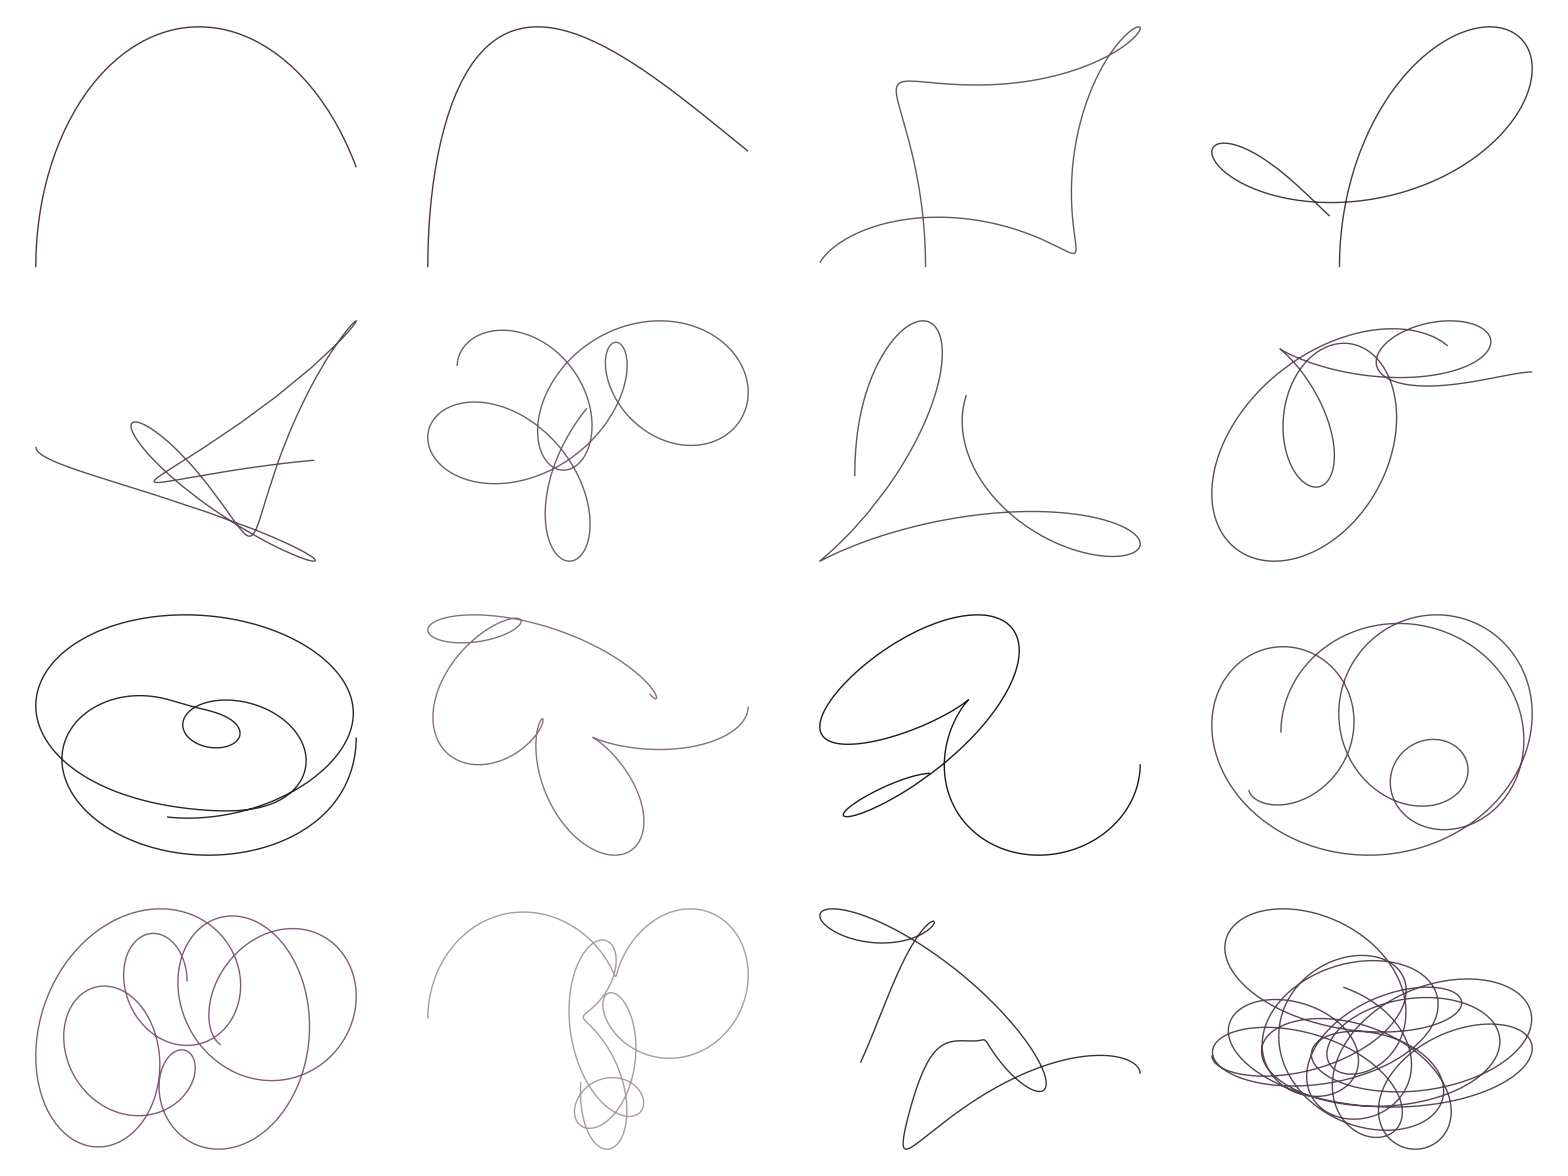

```mathematica
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
max=First@Quiet@FindMaximum[{curv,0≤t≤10},{t,5}];
min=First@Quiet@FindMinimum[{curv,0≤t≤10},{t,5}];
ParametricPlot[ReIm[f],{t,0,tf},Axes->False,PlotRange->All,ColorFunction->Function[{x,y,t},ColorData["FuchsiaTones"][Rescale[curv,{min,max}]]],ColorFunctionScaling->False,PlotStyle->Thick]],{tf,1,32,2}],4]]
```